```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
<<Wolfram`QuantumFramework`SecondQuantization`
```

## Measurements

```mathematica
a:=AnnihilationOperator[]
```

### Fock measurement

```mathematica
state = CoherentState[][2.1]["Normalize"]
```

QuantumState[…]

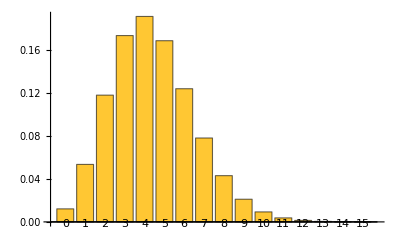

```mathematica
state["ProbabilityPlot"]
```

Operator for measuring in Fock basis:

```mathematica
fockMeasure = QuantumMeasurementOperator[SuperDagger[a]@a];
```

Single outcome:

```mathematica
o = fockMeasure[state]["SimulatedMeasurement"][[1,2,1]]
```

3

200 shots:

```mathematica
outcomes = QuantumMeasurementSimulation[state,{fockMeasure},200]//Last
```

{2,13,27,19,48,35,20,20,9,7,0,0,0,0,0,0}

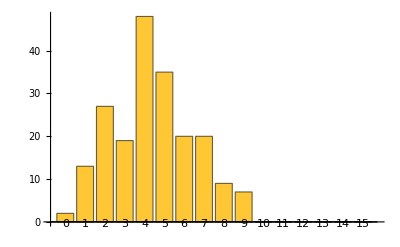

```mathematica
BarChart[outcomes,ChartLabels->Table[Ket[{i}],{i,0,$FockSize-1}]]
```

1000 shots:

```mathematica
outcomes = QuantumMeasurementSimulation[state,{fockMeasure},1000]//Last
```

{9,42,116,154,203,178,134,79,51,16,10,6,2,0,0,0}

```mathematica
outcomes = fockMeasure[state]["SimulatedCounts",1000]
```

{14,51,108,173,214,173,136,71,29,20,9,1,1,0,0,0}

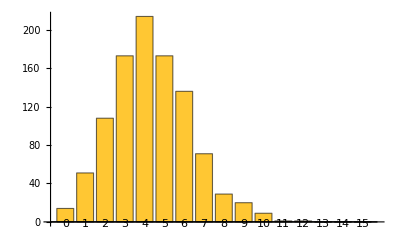

```mathematica
BarChart[outcomes,ChartLabels->Table[Ket[{i}],{i,0,$FockSize-1}]]
```

### Multimode Fock measurement

```mathematica
state = BeamSplitterOperator[{π/4.,π/2}]@FockState[{5,0}]
```

(0.+0.176777 ⅈ)05+(0.395285+0. ⅈ)14+(0.-0.559017 ⅈ)23+(-0.559017+0. ⅈ)32+(0.+0.395285 ⅈ)41+(0.176777+0. ⅈ)50

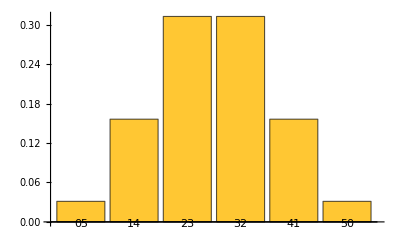

```mathematica
state["ProbabilityPlot"]
```

```mathematica
probs =state["Probability"]
```

<|05→0.03125,14→0.15625,23→0.3125,32→0.3125,41→0.15625,50→0.03125|>

500 shots:

```mathematica
{labels,probs}=Comap[{Keys,Values},state["Probability"]];
samples=RandomChoice[probs->labels,500];
```

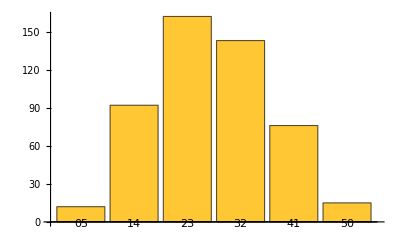

```mathematica
BarChart[KeySort@Counts[samples],ChartLabels->labels]
```